# Working with Images Johnathan Lovett Dr. Nabil Lawandy 1 August 2019

# Graphing the Differential Equation

## Parametric Plot (S vs ΔX)

```mathematica
nnn=ParametricNDSolve[{x1''[t]-eq1==0,x2''[t]-eq2==0,x1[0]==-10^-10, x1'[0]==0,x2[0]==10^-10,x2'[0]==0},x2'[t]*τ,{t,0,t3},{x2[t]-x1[t]}]
```

```mathematica
ParametricPlot[{Evaluate[x2[t]-x1[t]/.n],Evaluate[x2'[t]*τ/.ntwoprime]},{t,0,t3}]
```

-Graphics-

## Range of Validity for Delayed Image Model

```mathematica
Clear[t3]
nn=NDSolve[{x1''[t]-eq1==0,x2''[t]-eq2==0,x1[0]==-10^-10, x1'[0]==0,x2[0]==10^-10,x2'[0]==0},x2[t]-x1[t],{t,0,10^-1}]
Manipulate[Plot[Evaluate[{x2[t]-x1[t]}/.nn],{t,0,t6},PlotRange->All],{t6,10^-16,10^-10}]
```

{{-x1[t]+x2[t]→-InterpolatingFunction[{{0., 0.1}}, <>][t]+InterpolatingFunction[{{0., 0.1}}, <>][t]}}

## Confirmation That dX/dt * T is Greater Than X When Displaying Unphysical Behavior of Moving Faster than Non-delayed Image

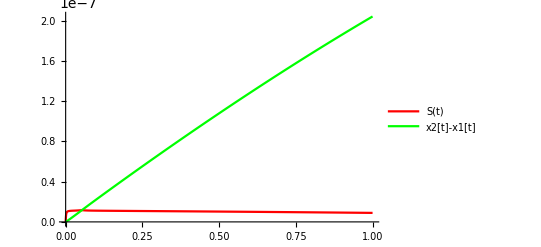

```mathematica
Show[Plot[Evaluate[x2'[t]*τ/.ntwoprime],{t,0,10^-13},PlotRange->All,PlotStyle->Red,PlotLegends->{"S(t)"}],Plot[Evaluate[x2[t]-x1[t]/.n],{t,0,10^-13},PlotRange->All,PlotStyle->Green,PlotLegends->{"x2[t]-x1[t]"}]]
```

## x2[t] - x1[t] for Time Interval [0,10^-11]

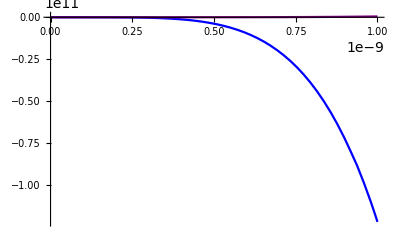

```mathematica
Show[Plot[Evaluate[x2[t]-x1[t]/.n],{t,0,10^-9},PlotRange->All,PlotStyle->Blue],Plot[Evaluate[x2[t]-x1[t]/.nos],{t,0,10^-9},PlotRange->All,PlotStyle->Purple,PlotLabel->{"PURPLE IS NO S"}]]
```

## x2’[t]-x1’[t] for Time Interval [0,10^-9]

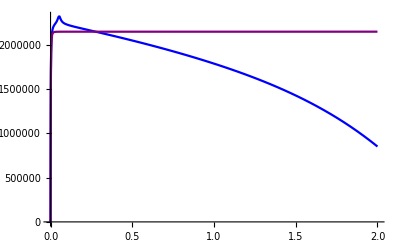

```mathematica
Show[Plot[Evaluate[x2'[t]-x1'[t]/.nprime],{t,0,2*10^-13},PlotStyle->Blue],Plot[Evaluate[x2'[t]-x1'[t]/.nosprime],{t,0,2*10^-13},PlotStyle->Purple,PlotRange->All]]
```

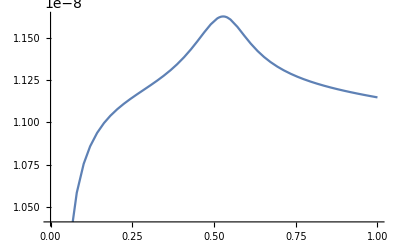

```mathematica
Plot[Evaluate[x2'[t]*10^-14/.ntwoprime],{t,0,10^-14}]
```

## Potential Graphs and Minimums for Two Particles Moving

## Two Charges Moving in the Same Direction

Plot Manipulation: Well appears to begin slightly at α = √2

```mathematica
Manipulate[Plot[(-ξ/(√(4+α^2))+1/β-ξ/(2 √(4+(-α+β)^2))-ξ/(2 √(4+(α+β)^2))),{β,1,20},PlotRange->All],{α,0.1,50},{ξ,0,1}]
```

Minimum Manipulation: Function blows up at α < or = √2

```mathematica
Manipulate[NArgMin[{-1/(√(4+α^2))+1/β-1/(2 √(4+(-α+β)^2))-1/(2 √(4+(α+β)^2)), 1 < β < 500}, {β}], 
  {{α, 1}, 0, 12}]
```

## Two Charges Moving in Opposite Directions

```mathematica
Manipulate[Plot[(-ξ/(√(4+α^2))+1/β-ξ/(√(4+(-α+β)^2))),{β,1,20},PlotRange->All],{α,0.1,50},{ξ,0,1}]
```

Minimum Appears at α= 1.81 . Note that function blows up at α = 0.

```mathematica
Manipulate[NArgMin[{-1/(√(4+α^2))+1/β-1/(√(4+(-α+β)^2)), 1 < β }, {β}], 
  {α, 0, 12}]
```

Equation and Variable Setting

```mathematica
Clear[k,xo,s1,s2,ϵo,q,d,τ,m,n,t,eq1,eq2]
Clear[Derivative]
q= 1.6021765×10^−19
τ=10^-14
m=9*10^-31
d=1 * 10^-9
ϵo=8.8541878128×10^−12

k=(1/ (4  π ϵo))
s1=τ x1'[t]
s2=τ x2'[t]
xo=(x2[t]-x1[t])

t3=10^-13



eq1=-(k*q^2 / m) * (1/xo^2) - (k *q^2 / m)* (s1/ (s1^2 + 4d^2)^(3/2)) + (k *q^2 / m)* ((xo-s2)/ ((xo-s2)^2 + 4d^2)^(3/2))

eq2 = (k*q^2 / m) * (1/xo^2) - (k *q^2 / m)* (s2/ (s2^2 + 4d^2)^(3/2)) - (k *q^2 / m)* ((xo+s1)/ ((xo+s1)^2 + 4d^2)^(3/2))



n=NDSolve[{x1''[t]-eq1==0,x2''[t]-eq2==0,x1[0]==-10^-10, x1'[0]==0,x2[0]==10^-10,x2'[0]==0},x2[t]-x1[t],{t,0,t3}]

ntwoprime=NDSolve[{x1''[t]-eq1==0,x2''[t]-eq2==0,x1[0]==-10^-10, x1'[0]==0,x2[0]==10^-10,x2'[0]==0},x2'[t],{t,0,t3}]

nprime=NDSolve[{x1''[t]-eq1==0,x2''[t]-eq2==0,x1[0]==-10^-10, x1'[0]==0,x2[0]==10^-10,x2'[0]==0}, x2'[t]-x1'[t],{t,0,t3}]


s12=0
s22=0


meq1=-(k*q^2 / m) * (1/xo^2) - (k *q^2 / m)* (s12/ (s12^2 + 4d^2)^(3/2)) + (k *q^2 / m)* ((xo-s22)/ ((xo-s22)^2 + 4d^2)^(3/2))

meq2 = (k*q^2 / m) * (1/xo^2) - (k *q^2 / m)* (s22/ (s22^2 + 4d^2)^(3/2)) - (k *q^2 / m)* ((xo+s12)/ ((xo+s12)^2 + 4d^2)^(3/2))



nos=NDSolve[{x1''[t]-meq1==0,x2''[t]-meq2==0,x1[0]==-10^-10, x1'[0]==0,x2[0]==10^-10,x2'[0]==0},x2[t]-x1[t],{t,0,t3}]

nosprime=NDSolve[{x1''[t]-meq1==0,x2''[t]-meq2==0,x1[0]==-10^-10, x1'[0]==0,x2[0]==10^-10,x2'[0]==0},x2'[t]-x1'[t],{t,0,t3}]
```

1.60218×10^-19

1/100000000000000

9/10000000000000000000000000000000

1/1000000000

8.85419×10^-12

8.98755×10^9

x1'[t]/100000000000000

x2'[t]/100000000000000

-x1[t]+x2[t]

1/10000000000000

-256.342/(-x1[t]+x2[t])^2-(2.56342×10^-12 x1'[t])/((1/250000000000000000+x1'[t]^2/10000000000000000000000000000)^(3/2))+(256.342 (-x1[t]+x2[t]-x2'[t]/100000000000000))/((1/250000000000000000+(-x1[t]+x2[t]-x2'[t]/100000000000000)^2)^(3/2))

256.342/(-x1[t]+x2[t])^2-(256.342 (-x1[t]+x2[t]+x1'[t]/100000000000000))/((1/250000000000000000+(-x1[t]+x2[t]+x1'[t]/100000000000000)^2)^(3/2))-(2.56342×10^-12 x2'[t])/((1/250000000000000000+x2'[t]^2/10000000000000000000000000000)^(3/2))

{{-x1[t]+x2[t]→-                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]+                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]}}

{{x2'[t]→                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]}}

{{-x1'[t]+x2'[t]→-                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]+                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]}}

0

0

0.-256.342/(-x1[t]+x2[t])^2+(256.342 (-x1[t]+x2[t]))/((1/250000000000000000+(-x1[t]+x2[t])^2)^(3/2))

0.+256.342/(-x1[t]+x2[t])^2-(256.342 (-x1[t]+x2[t]))/((1/250000000000000000+(-x1[t]+x2[t])^2)^(3/2))

{{-x1[t]+x2[t]→-                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]+                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]}}

{{-x1'[t]+x2'[t]→-                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]+                                 -13
InterpolatingFunction[{{0., 1. 10   }}, <>][t]}}

```mathematica
ParametricPlot[{x2'[t]*τ/.ntwoprime },{t,0,10^-12}]
```

-Graphics-